# Electrochemical PCET modeling

## Copyright 2005-2013 Hammes-Schiffer Group, University of Illinois at Urbana-Champaign; (Alexander Soudackov, Brian Solis, Samantha Horvath, Ben Auer)

Change to the directory containing this notebook:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Zach-Hydrogen-discharge/Mathematica

Include all the function from the MathPCETwithET package (must be in the same directory):

```mathematica
Needs["MathPCETwithET`"]
```

## Parameters

```mathematica
T=298.15; (* Temperature in K *)
Vel=1.0; (* Electronic coupling in kcal/mol (does not affect KIE) *)
λs=39.00; (* Total reorganization energy in kcal/mol - should be determined separately *)
```

## Functions for current densities

```mathematica
?AnodicCurrentDensityMorse
```

AnodicCurrentDensityMorse[eta,lambda,MR,omega,dR,Beta1,DE1,Beta2,DE2,mumax,numax,d,T]
Parameters:
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
omega - frequency of the coupling between the oscillators in wavenumbers;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
Beta1 - beta parameter for oscillator on the left in inverse Bohr;
DE1 - dissociation energy of the oscillator on the left in kcal/mol;
Beta2 - beta parameter for oscillator on the right in inverse Bohr;
DE2 - dissociation energy of the oscillator on the right in kcal/mol;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Options:
M -> mass of the particle in Daltons (Default - mass of the proton);
Step -> step to take in numerical differentiaion (Default - 0.0001);
Returns the current density for oxidation in the Morse approximation

```mathematica
?CathodicCurrentDensityMorse
```

CathodicCurrentDensityMorse[eta,lambda,MR,omega,dR,Beta1,DE1,Beta2,DE2,mumax,numax,d,T]
Parameters:
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
omega - frequency of the coupling between the oscillators in wavenumbers;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
Beta1 - beta parameter for oscillator on the left in inverse Bohr;
DE1 - dissociation energy of the oscillator on the left in kcal/mol;
Beta2 - beta parameter for oscillator on the right in inverse Bohr;
DE2 - dissociation energy of the oscillator on the right in kcal/mol;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Options:
M -> mass of the particle in Daltons (Default - mass of the proton);
Step -> step to take in numerical differentiaion (Default - 0.0001);
Returns the current density for reduction in the Morse approximation

```mathematica
?TotalCurrentDensityMorse
```

TotalCurrentDensityMorse[eta,lambda,MR,omega,dR,Beta1,DE1,Beta2,DE2,mumax,numax,d,T,Cox,Cred]
Parameters:
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
omega - frequency of the coupling between the oscillators in wavenumbers;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
Beta1 - beta parameter for oscillator on the left in inverse Bohr;
DE1 - dissociation energy of the oscillator on the left in kcal/mol;
Beta2 - beta parameter for oscillator on the right in inverse Bohr;
DE2 - dissociation energy of the oscillator on the right in kcal/mol;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Cox - concentration of the oxidized complex (any consistent units);
Cred - concentration of the reduced complex (any consistent units);
Options:
M -> mass of the particle in Daltons (Default - mass of the proton);
Step -> step to take in numerical differentiaion (Default - 0.0001);
Returns the total current density for the Morse approximation

```mathematica
?AnodicCurrentDensityHarmonic
```

AnodicCurrentDensityHarmonic[eta,lambda,MR,dR,omega,omega1,omega2,mumax,numax,d,T]
Parameters:
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
omega - frequency of the coupling between the oscillators in wavenumbers;
omega1 - frequency of oscillator on the left in wavenumbers;
omega2 - frequency of oscillator on the right in wavenumbers;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Options:
M -> mass of the particle in Daltons (Default - mass of the proton);
Returns the current density for oxidation in the harmonic approximation

```mathematica
?CathodicCurrentDensityHarmonic
```

CathodicCurrentDensityHarmonic[eta,lambda,MR,dR,omega,omega1,omega2,mumax,numax,d,T]
Parameters:
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
omega - frequency of the donor-acceptor mode in wavenumbers;
omega1 - frequency of oscillator on the left in wavenumbers;
omega2 - frequency of oscillator on the right in wavenumbers;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Options:
M -> mass of the particle in Daltons (Default - mass of the proton);
Returns the current density for reduction in the harmonic approximation

```mathematica
?TotalCurrentDensityHarmonic
```

TotalCurrentDensityHarmonic[eta,lambda,MR,dR,omega,omega1,omega2,mumax,numax,d,T,Cox,Cred]
Parameters:
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
omega - frequency of the coupling between the oscillators in wavenumbers;
omega1 - frequency of oscillator on the left in wavenumbers;
omega2 - frequency of oscillator on the right in wavenumbers;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Cox - concentration of the oxidized complex (any consistent units);
Cred - concentration of the reduced complex (any consistent units);
M -> mass of the particle in Daltons (Default - mass of the proton);
Returns the total current density for the harmonic approximation

```mathematica
?AnodicCurrentDensityFGH
```

AnodicCurrentDensityFGH[fghlist,eta,lambda,MR,dR,omega,mumax,numax,d,T]
Parameters:
fghList - nested list with energies, wavefunctions, overlap integrals and alphas;
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
omega - frequency of the coupling between the oscillators in wavenumbers;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Options:
Returns the current density for oxidation for general proton potentials

```mathematica
?CathodicCurrentDensityFGH
```

CathodicCurrentDensityFGH[fghlist,eta,lambda,MR,dR,omega,mumax,numax,d,T]
Parameters:
fghList - nested list with energies, wavefunctions, overlap integrals and alphas;
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
omega - frequency of the coupling between the oscillators in wavenumbers;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Options:
Returns the current density for reduction for general proton potentials

```mathematica
?TotalCurrentDensityFGH
```

TotalCurrentDensityFGH[fghlist,eta,lambda,MR,dR,omega,mumax,numax,d,T,Cox,Cred]
Parameters:
fghList - nested list with energies, wavefunctions, overlap integrals and alphas;
eta - overpotential in volts;
lambda - solvent reorganization energy in kcal/mol;
MR - reduced mass of the donor-acceptor mode in Daltons;
dR - distance between the equlibrium value of the R mode at product state and the reactant state (Rnu-Rmu) in Bohr;
omega - frequency of the coupling between the oscillators in wavenumbers;
mumax - maximum quantum number of oscillator on the left;
numax - maximum quantum number of oscillator on the right;
d - distance between the minima of the displaced potentials in bohr;
T - temperature in Kelvin;
Cox - concentration of the oxidized complex (any consistent units);
Cred - concentration of the reduced complex (any consistent units);
Returns the total current density for general proton potentials

## Rate constant expressions

Some additional functions:

```mathematica
AnodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=Module[{eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns},Ns=Length[fghlist[[1,1]]];
If[mumax+1>Ns||numax+1>Ns,Message[AnodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]],{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]],{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
SS=NIntegrate[Sum[(Exp[-energymu[mu]/(kb*T)]/Z1)*ov[mu,nu]^2*Sqrt[Pi/(kb*T*lam)]*(1-Fermi[eps,T])*Exp[-(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]+eps-eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
10^12*(Vel*kcal2au)^2*SS/au2ps];
```

```mathematica
CathodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=Module[{eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns},Ns=Length[fghlist[[1,1]]];
If[mumax+1>Ns||numax+1>Ns,Message[CathodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]],{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]],{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
SS=NIntegrate[Sum[(Exp[-energynu[nu]/(kb*T)]/Z2)*ov[mu,nu]^2*Sqrt[Pi/(kb*T*lam)]*Fermi[eps,T]*Exp[-(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]-eps+eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
10^12*(Vel*kcal2au)^2*SS/au2ps];
```

## Tables with rate contributions

Functions building the tables with rate contributions:

```mathematica
TableAnodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=
Module[{emu0,enu0,headings,info,ktotal,eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns,kmunu,dUmunu,Eamunu,Pmu,S2munu},
headings={"μ","ν","P_μ",strs2munu,"ΔU_μν",strdgddmunu<>"(η)","exp[-β"<>strdgddmunu<>"(η)"<>"]","k_μν(η)","%"};
Ns=Length[fghlist[[1,1]]];
emu0=kcal2au*fghlist[[1]][[1,1]];
enu0=kcal2au*fghlist[[2]][[1,1]];
If[mumax+1>Ns||numax+1>Ns,Message[AnodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]]-emu0,{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]]-enu0,{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
Array[kmunu,{mumax+1,numax+1},0];
Array[dUmunu,{mumax+1,numax+1},0];
Array[Eamunu,{mumax+1,numax+1},0];
Array[Pmu,mumax+1,0];
Do[Pmu[mu]=Exp[-energymu[mu]/(kb*T)]/Z1,{mu,0,mumax}];
Array[S2munu,{mumax+1,numax+1},0];
Do[S2munu[mu,nu]=ov[mu,nu]^2,{mu,0,mumax},{nu,0,numax}];
SS=NIntegrate[Sum[Pmu[mu]*S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*(1-Fermi[eps,T])*Exp[-(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]+eps-eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
ktotal=10^12*(Vel*kcal2au)^2*SS/au2ps;

Do[
dUmunu[mu,nu]=energynu[nu]-energymu[mu]; (*+kb*T*Log[Z2/Z1]-eta*ev2au;*)
Eamunu[mu,nu]=(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]-eta*ev2au+lam)^2/(4*lam);
kmunu[mu,nu]=10^12*(Vel*kcal2au)^2*NIntegrate[S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*(1-Fermi[eps,T])*Exp[-(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]+eps-eta*ev2au+lam)^2/(4*kb*T*lam)],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20]/au2ps,
{nu,0,numax},{mu,0,mumax}];
info="kT Log[Z_2/Z_1]="<>ToString[NumberForm[au2kcal*kb*T*Log[Z2/Z1],4]]<>" kcal/mol; λ="<>ToString[NumberForm[lambda,4]]<>" kcal/mol; η="<>ToString[NumberForm[eta,4]]<>" V; k_a(total)="<>ToString[NumberForm[ktotal,6]]<>" s^-1";

Grid[Join[{
{info,SpanFromLeft}},
{headings},
Flatten[Table[{
mu,
nu,
ScientificForm[Pmu[mu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[S2munu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[dUmunu[mu,nu]*au2kcal,{6,3}],
PaddedForm[Eamunu[mu,nu]*au2kcal,{6,3}],
ScientificForm[Exp[-Eamunu[mu,nu]/(kb*T)],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[kmunu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[Pmu[mu]*kmunu[mu,nu]*100/ktotal,{7,3}]
},{mu,0,mumax},{nu,0,numax}],1]],Frame->All,Spacings->{Automatic,1}]
];
```

```mathematica
TableCathodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=
Module[{emu0,enu0,headings,info,ktotal,eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns,kmunu,dUmunu,Eamunu,Pnu,S2munu},
headings={"ν","μ","P_ν",strs2munu,"ΔU_μν",strdgddmunu<>"(η)","exp[-β"<>strdgddmunu<>"(η)"<>"]","k_νμ(η)","%"};
Ns=Length[fghlist[[1,1]]];
emu0=kcal2au*fghlist[[1]][[1,1]];
enu0=kcal2au*fghlist[[2]][[1,1]];
If[mumax+1>Ns||numax+1>Ns,Message[AnodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]]-emu0,{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]]-enu0,{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
Array[kmunu,{mumax+1,numax+1},0];
Array[dUmunu,{mumax+1,numax+1},0];
Array[Eamunu,{mumax+1,numax+1},0];
Array[Pnu,mumax+1,0];
Do[Pnu[nu]=Exp[-energynu[nu]/(kb*T)]/Z2,{nu,0,numax}];
Array[S2munu,{mumax+1,numax+1},0];
Do[S2munu[mu,nu]=ov[mu,nu]^2,{mu,0,mumax},{nu,0,numax}];
SS=NIntegrate[Sum[Pnu[nu]*S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*Fermi[eps,T]*Exp[-(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]-eps+eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
ktotal=10^12*(Vel*kcal2au)^2*SS/au2ps;

Do[
dUmunu[mu,nu]=-energynu[nu]+energymu[mu];(*-kb*T*Log[Z2/Z1]+eta*ev2au;*)
Eamunu[mu,nu]=(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]+eta*ev2au+lam)^2/(4*lam);
kmunu[mu,nu]=10^12*(Vel*kcal2au)^2*NIntegrate[S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*Fermi[eps,T]*Exp[-(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]-eps+eta*ev2au+lam)^2/(4*kb*T*lam)],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20]/au2ps,
{nu,0,numax},{mu,0,mumax}];
info="kT Log[Z_2/Z_1]="<>ToString[NumberForm[au2kcal*kb*T*Log[Z2/Z1],4]]<>" kcal/mol; λ="<>ToString[NumberForm[lambda,4]]<>" kcal/mol; η="<>ToString[NumberForm[eta,4]]<>" V; k_c(total)="<>ToString[ScientificForm[ktotal,6]]<>" s^-1";

Grid[Join[{
{info,SpanFromLeft}},
{headings},
Flatten[Table[{
nu,
mu,
ScientificForm[Pnu[nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[S2munu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[dUmunu[mu,nu]*au2kcal,{6,3}],
PaddedForm[Eamunu[mu,nu]*au2kcal,{6,3}],
ScientificForm[Exp[-Eamunu[mu,nu]/(kb*T)],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[kmunu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[Pnu[nu]*kmunu[mu,nu]*100/ktotal,{7,3}]
},{mu,0,mumax},{nu,0,numax}],1]],Frame->All,Spacings->{Automatic,1}]
];
```

## R-dependences of P(R)

Effective force constant for donor-acceptor motion
and equilibrium donor-acceptor distance (in Å)

```mathematica
(*kaeff=0.046003586;*)
(* Fujita's system, oxidized geometry: kceff=0.031412530;*)
kceff=0.031412530;
(*keff=0.5*(kaeff+kceff);*)
(*Rav0=0.5*(2.57131+2.55066)/bohr2a;*)
Req=2.61892/bohr2a;
Ωeq=Sqrt[(2.0*π*kb*T)/kceff]*bohr2a;
```

```mathematica
au2cm √(kceff/(7 Dalton))
```

344.354

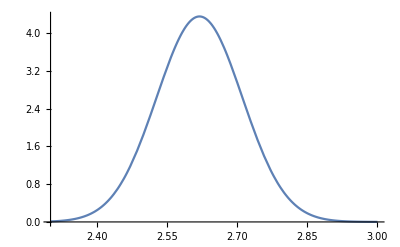

```mathematica
P[R_]=Exp[-(0.5*kceff*((R/bohr2a)-Req)^2)/(kb*T)]/Ωeq;
Plot[P[R],{R,2.3,3.0},PlotRange->All]
```

Check normalization:

```mathematica
NIntegrate[P[R],{R,-∞,∞}]
```

1.

## R (O-N) distances (Å)

Donor-Acceptor Distances:

```mathematica
R211=2.11892;
R221=2.21892;
R231=2.31892;
R241=2.41892;
R251=2.51892;
R261=2.61892;
R271=2.71892;
R281=2.81892;
R291=2.91892;
R301=3.01892;
R311=3.11892;
```

## Reactant (1a) and product (2b) wavefunctions - H and D

Calculate vibrational states for all PT profiles (take a bit of time):
(Note that the package settings assume that the executable fgh_bspline.bin is found in /usr/local/bspline/bin)

```mathematica
waveH211=FGHWavefunctions["profiles/211892-profile-red-ox-au.dat",1024,15];
waveH221=FGHWavefunctions["profiles/221892-profile-red-ox-au.dat",1024,15];
waveH231=FGHWavefunctions["profiles/231892-profile-red-ox-au.dat",1024,15];
waveH241=FGHWavefunctions["profiles/241892-profile-red-ox-au.dat",1024,15];
waveH251=FGHWavefunctions["profiles/251892-profile-red-ox-au.dat",1024,15];
waveH261=FGHWavefunctions["profiles/261892-profile-red-ox-au.dat",1024,15];
waveH271=FGHWavefunctions["profiles/271892-profile-red-ox-au.dat",1024,15];
waveH281=FGHWavefunctions["profiles/281892-profile-red-ox-au.dat",1024,15];
waveH291=FGHWavefunctions["profiles/291892-profile-red-ox-au.dat",1024,15];
waveH301=FGHWavefunctions["profiles/301892-profile-red-ox-au.dat",1024,15];
waveH311=FGHWavefunctions["profiles/311892-profile-red-ox-au.dat",1024,15];
```

```mathematica
waveD211=FGHWavefunctions["profiles/211892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD221=FGHWavefunctions["profiles/221892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD231=FGHWavefunctions["profiles/231892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD241=FGHWavefunctions["profiles/241892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD251=FGHWavefunctions["profiles/251892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD261=FGHWavefunctions["profiles/261892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD271=FGHWavefunctions["profiles/271892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD281=FGHWavefunctions["profiles/281892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD291=FGHWavefunctions["profiles/291892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD301=FGHWavefunctions["profiles/301892-profile-red-ox-au.dat",1024,15,M->MassD];
waveD311=FGHWavefunctions["profiles/311892-profile-red-ox-au.dat",1024,15,M->MassD];
```

```mathematica
?FGHWavefunctions
```

Fourier Grid Hamiltonian calculations of the wavefunctions and overlap integrals.
FGHWavefunctions[file_,nGridPoints_,nStates_].
Parameters:
file - name of the file with the potential data (three columns: x(A) Ureactant(Hartree) Uproduct(Hartree));
nGridPoints - number of grid points (should be power of two);
nStates - number of vibrational states in each well to calculate.
Options:
M -> mass of the particle in Daltons (Default - mass of the proton).
Output:
Returns a nested list of the following structure:
(
 (reactantEnergies_list, reactantPotential_matrix, reactantWavefunctions_matrix),
 (productEnergies_list, productPotential_matrix, productWavefunctions_matrix),
 overlap_matrix,
 alpha_matrix
)
where
xxxEnergies_list - is a list (vector) of length nStates;
xxxPotential_matrix - a 2D-list (table) of the splined potential [nGridPoints by 2];
xxxWavefunctions_matrix - a 2D-list (matrix)  [nStates by nGridPoints];
overlap_matrix - 2D-list (matrix) of overlap integrals [nStates by nStates];
alpha_matrix - 2D-list (matrix) of alpha-parameters [nStates by nStates].

Check (visualize) the wavefunctions:

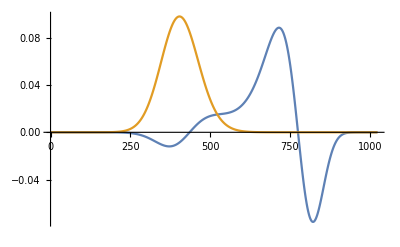

```mathematica
GraphicsRow[
{ListLinePlot[{waveH261⟦1,3,3⟧,waveH261⟦2,3,1⟧},PlotRange->All]},
ImageSize->Medium
]
```

More elaborate plots for checking that everything makes sense:

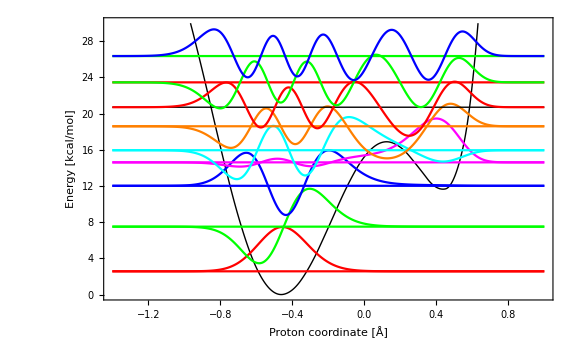

```mathematica
wavelist=waveH261;
ListLinePlot[{
Table[{wavelist[[2,2]][[i,1]],wavelist[[2,2]][[i,2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]+50*wavelist[[2,3,1]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]+50*wavelist[[2,3,2]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]+50*wavelist[[2,3,3]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]+50*wavelist[[2,3,4]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]+50*wavelist[[2,3,5]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]+50*wavelist[[2,3,6]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],
Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[7]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[7]]+50*wavelist[[2,3,7]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[8]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[8]]+50*wavelist[[2,3,8]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[9]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[9]]+50*wavelist[[2,3,9]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}]
},
PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

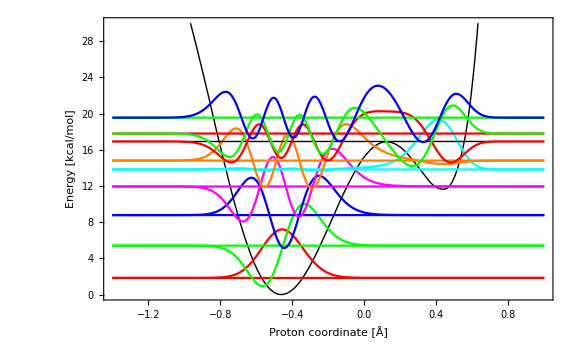

```mathematica
wavelist=waveD261;
ListLinePlot[{
Table[{wavelist[[2,2]][[i,1]],wavelist[[2,2]][[i,2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]+50*wavelist[[2,3,1]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]+50*wavelist[[2,3,2]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]+50*wavelist[[2,3,3]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]+50*wavelist[[2,3,4]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]+50*wavelist[[2,3,5]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]+50*wavelist[[2,3,6]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],
Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[7]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[7]]+50*wavelist[[2,3,7]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[8]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[8]]+50*wavelist[[2,3,8]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[9]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[9]]+50*wavelist[[2,3,9]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}]
},
PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

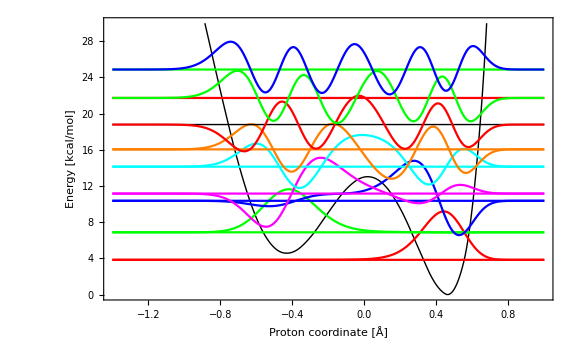

```mathematica
wavelist=waveH261;
ListLinePlot[{
Table[{wavelist[[1,2]][[i,1]],wavelist[[1,2]][[i,2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]+50*wavelist[[1,3,1]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]+50*wavelist[[1,3,2]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]+50*wavelist[[1,3,3]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]+50*wavelist[[1,3,4]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]+50*wavelist[[1,3,5]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]+50*wavelist[[1,3,6]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],
Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[7]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[7]]+50*wavelist[[1,3,7]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[8]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[8]]+50*wavelist[[1,3,8]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[9]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[9]]+50*wavelist[[1,3,9]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}]
},
PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

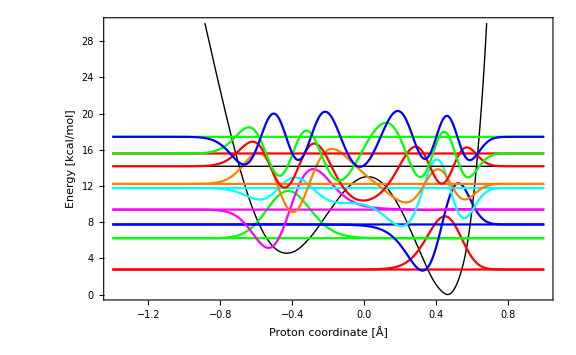

```mathematica
wavelist=waveD261;
ListLinePlot[{
Table[{wavelist[[1,2]][[i,1]],wavelist[[1,2]][[i,2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]+50*wavelist[[1,3,1]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]+50*wavelist[[1,3,2]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]+50*wavelist[[1,3,3]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]+50*wavelist[[1,3,4]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]+50*wavelist[[1,3,5]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]+50*wavelist[[1,3,6]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],
Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[7]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[7]]+50*wavelist[[1,3,7]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[8]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[8]]+50*wavelist[[1,3,8]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[9]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[9]]+50*wavelist[[1,3,9]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}]
},
PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

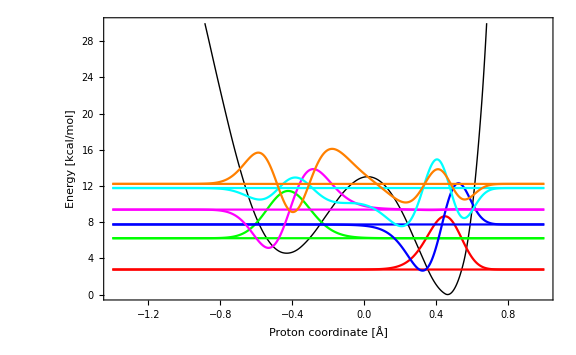

```mathematica
wavelist=waveD261;
ListLinePlot[{
Table[{wavelist[[1,2]][[i,1]],wavelist[[1,2]][[i,2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]+50*wavelist[[1,3,1]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]+50*wavelist[[1,3,2]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]+50*wavelist[[1,3,3]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]+50*wavelist[[1,3,4]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]+50*wavelist[[1,3,5]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]+50*wavelist[[1,3,6]][[i]]},
{i,1,Length[wavelist[[1,3,1]]]}]},
PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```